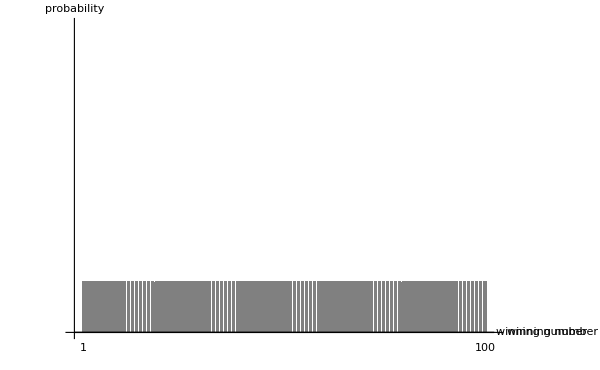

```mathematica
vX ={1};
vX1 = Table["",{98}];
vX2={100};
vX = Join[vX,vX1,vX2];
vProbabilityHigherVariance = Table[1/100,{100}];
g1=Show[BarChart[vProbabilityHigherVariance,BarSpacing->Large,PlotRange->{Automatic,{0,0.06}},AxesLabel->{"winning number "," probability "},BaseStyle->{FontSize->16},ChartStyle->{Gray},Ticks->{False,False}],ImagePadding->{{30,130},{30,30}},ImageSize->600,Epilog->{Text["1",Scaled[{0.04,-.03}]],Text["100",Scaled[{0.96,-.03}]]}]
```

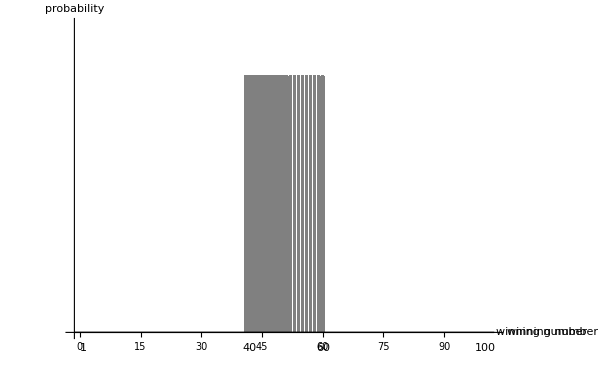

```mathematica
vProbabilityLowerVariance = Table[0,{40}];
vProbabilityLowerVariance1 = Table[1/20,{20}];
vProbabilityLowerVariance= Join[vProbabilityLowerVariance,vProbabilityLowerVariance1,vProbabilityLowerVariance];
g2=Show[BarChart[vProbabilityLowerVariance,PlotRange->{Automatic,{0,0.06}},BarSpacing->Large,AxesLabel->{"winning number "," probability "},Ticks->{True,False},BaseStyle->{FontSize->16},ChartStyle->{Gray}],ImagePadding->{{30,130},{30,30}},Epilog->{Text["1",Scaled[{0.04,-.03}]],Text["100",Scaled[{0.96,-.03}]],Text["40",Scaled[{0.42,-.03}]],Text["60",Scaled[{0.59,-.03}]]},ImageSize->600]
```

```mathematica
toPiecewise[wts_,x_]:=Piecewise[MapIndexed[{#1,x==#2[[1]]}&,wts]]
dLowVariance=ProbabilityDistribution[toPiecewise[vProbabilityLowerVariance,x],{x,1,100,1}];
```

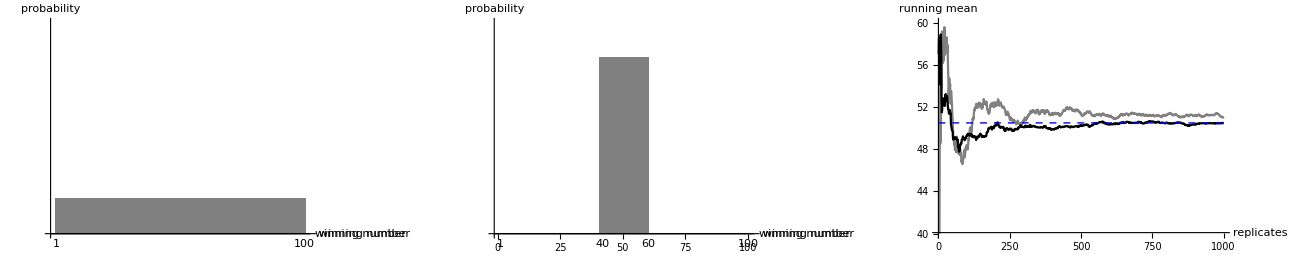

```mathematica
n = 1000;
vDataHigh=RandomVariate[DiscreteUniformDistribution[{1,100}],{n}];
vDataLow = RandomVariate[dLowVariance,{n}];
vMeanHigh=Accumulate[vDataHigh]/Table[i,{i,1,n}];
vMeanLow=Accumulate[vDataLow]/Table[i,{i,1,n}];
g3=ListLinePlot[vMeanHigh,PlotStyle->Gray,PlotRange->{Automatic,{40,60}},Epilog->{Dashed,Blue,Line[{{0,50.5},{1000,50.5}}]},BaseStyle->{FontSize->16},AxesLabel->{"replicates ","running  mean "}];
g4=ListLinePlot[vMeanLow,PlotStyle->Black,PlotRange->{Automatic,{40,60}},Epilog->{Dashed,Blue,Line[{{0,50.5},{1000,50.5}}]},BaseStyle->{FontSize->16},AxesLabel->{"rolls ","running  mean "}];
g5=Show[g3,g4,ImagePadding->{{60,130},{30,30}},ImageSize->600];
Show[GraphicsRow[{g1,g2,g5}],ImageSize->1300]
```

```mathematica
Variance[DiscreteUniformDistribution[{1,100}]]
```

3333/4

```mathematica
N[3333/4]
```

833.25

```mathematica
Rationalize[Total[Table[(1/6)(i-3.5)^2,{i,1,6}]]]
```

35/12

```mathematica
Variance[dLowVariance]
```

1058511/4000

```mathematica
N[1058511/4000]
```

264.628

```mathematica
dLowVariance
```